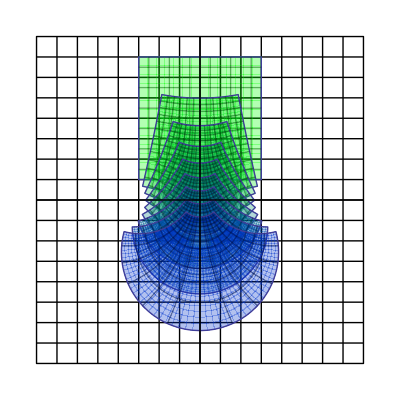

```mathematica
b=Show[ParametricPlot[{x,y},{x,-2,2},{y,-2,2},Mesh->15,BoundaryStyle->Black,MeshStyle->Black,PlotStyle->Directive[Opacity[0]]],Table[ParametricPlot[{Re[(+ⅈ(x+ⅈ y)+Tan[a/2])/(Tan[a/2](x+ⅈ y)+ⅈ)],Im[(+ⅈ(x+ⅈ y)+Tan[a/2])/(Tan[a/2](x+ⅈ y)+ⅈ)]},{x,-0.75,0.75},{y,0.25,1.75},Mesh->11,PlotStyle->Directive[RGBColor[0,1-1/Pi a,1/Pi a],Opacity[0.3]]],{a,0,Pi-2Pi/10,Pi/10}],Graphics[{Thick,Line[{{-2,0},{2,0}}],Line[{{0,-2},{0,2}}]}],Axes->False,PlotRange->{{-2,2},{-2,2}},Frame->False]
```

```mathematica
Export["b.jpg",b,ImageResolution->600]
```

b.jpg